```mathematica
(*SetDirectory["/home/pavel/test/scopes/"];*)
data=Import["spinup.csv","CSV",HeaderLines->2];
data=Downsample[data,{80,1}];
{Length@data,data[[1]]}
```

{10000,{0.38,0.0058624,0.0000693126,0.00564922}}

```mathematica
data=data[[1;;8000]];
```

```mathematica
{time,Va,Vb,Vc}=dataᵀ;
time=(time-time[[1]])10^6;

PhaseVoltageDivisionRatio=7.964; (* Valid for the reference design *)
{Va,Vb,Vc}={Va,Vb,Vc}*PhaseVoltageDivisionRatio;

MaxVoltage=Max[{Va,Vb,Vc}];
MinVoltage=Min[{Va,Vb,Vc}];

V0=Table[(Min[{Va[[i]],Vb[[i]],Vc[[i]]}]+Max[{Va[[i]],Vb[[i]],Vc[[i]]}])/2,{i,Length@Va}];
V0=MovingAverage[Join[V0,ConstantArray[0,9]],10];
```

```mathematica
plots=Map[ListLinePlot[{{time,#[[1]]}ᵀ,{time,V0}ᵀ},
PlotTheme->"Detailed",
FrameLabel->{If[#[[3]],"Time, μs",None],#[[2]]},
PlotStyle->Thickness[0.0015],
ImageSize->800,
AspectRatio->1/4,
PlotRange->{{MinVoltage,MaxVoltage}}
]&,{
{Va,"Phase A voltage, V",False},
{Vb,"Phase B voltage, V",False},
{Vc,"Phase C voltage, V",True}}];

legend=LineLegend[{Blue,Orange},{"Phase voltage","Neutral"},LegendLayout->"Row"];
```

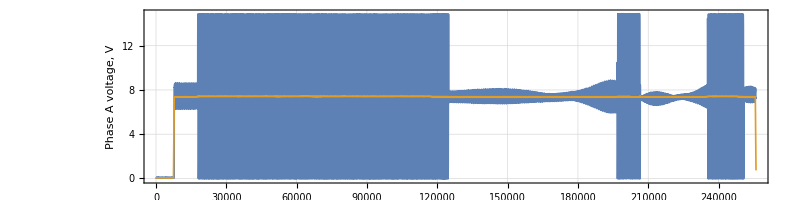
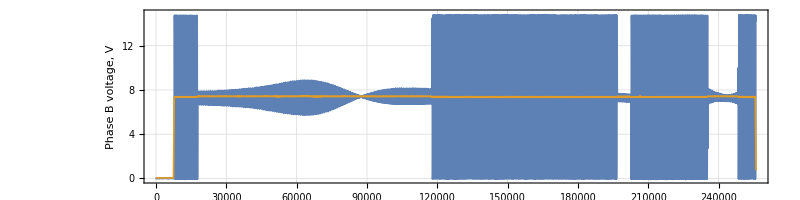
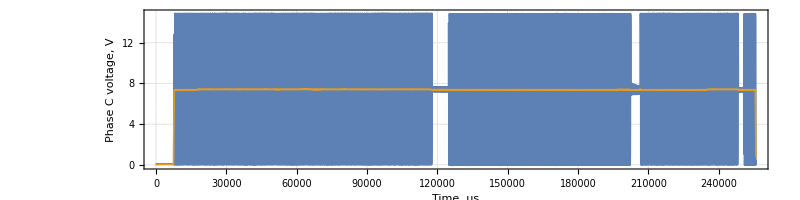

```mathematica
Column[Join[plots,{Pane[legend,Full,Alignment->Center]}]]
```